```mathematica
SetDirectory["/Users/gerardoalvarez/Desktop/Inelastic Dark Matter"]
```

/Users/gerardoalvarez/Desktop/Inelastic Dark Matter

```mathematica
(* mx in GeV, mphi in MeV, delta in KeV, velocity in km/s  *)
Sigmacalc[mx_,mphi_,delta_,vel_]:=Module[
(* Parameters *)
{
vlight=299792458/10^3,
diracmass=mx,
mediatormass=mphi,
δ=delta,
velo=vel
},
Print[velo];
Subscript[m, x]=diracmass;
Subscript[m, ϕ]=mediatormass;
v=velo/vlight;
Subscript[α, x]=1/10(*1/100(Subscript[m, x]/270)*); (* Dark Fine Structure Constant *)
b=(Subscript[α, x] Subscript[m, x])/Subscript[m, ϕ]; (* Dimensionless parameter. Range of Yukawa potential *)
a=v/(2 Subscript[α, x]); (* Dimensionless parameter ~ momentum of lighter species *)
c=√(a^2-(2δ)/(Subscript[m, x] Subscript[α, x]^2)); (* Dimensionless parameter ~ momentum of heavier species *)
(* Initialize angular momentum mode *)
l=0;
lmax=1500;

(* Initialize scattering cross sections *)
Subscript[σ, 11][l]=0.0;Subscript[σ, 21][l]=0.0;
Subscript[σT, 11][l]=0.0;Subscript[σT, 21][l]=0.0;
Subscript[σV, 11][l]=0.0;Subscript[σV, 21][l]=0.0;

Subscript[σ, 11][-1]=0.0;Subscript[σ, 21][-1]=0.0;

Subscript[σV, 11][1]=0.0;Subscript[σV, 21][1]=0.0;

(* Initialize cross section convergence *)
Subscript[xscon, 11] =1.0; 
Subscript[xscon, 21] =1.0; 

count=0; (* x section Convergence counter *)

While[count<10,

 Print["L → ",l]; 

(* Free particle solutions *)
Subscript[f, 1][x_]=  a x SphericalBesselJ[l,a x];
Subscript[g, 1][x_]= ⅈ a x SphericalHankelH1[l,a x];
Subscript[f, 2][x_]=  c x SphericalBesselJ[l,c x];
Subscript[g, 2][x_]= ⅈ c x SphericalHankelH1[l,c x];
(* Derivative of free particle solution of type g *)
Subscript[G, 1][x_]=D[Subscript[g, 1][x],x]/a;
Subscript[G, 2][x_]=D[Subscript[g, 2][x],x]/c;

max= 10 b; (* Initial Guess *)
min=10^-10 ; (* Initial Guess *)


(* Solve coupled equations *)func= NDSolve[{Subscript[u, 11]'[x]-a -a((Subscript[G, 1][x])/(Subscript[g, 1][x])+(Subscript[G, 1][x])/(Subscript[g, 1][x]))Subscript[u, 11][x] +(Subscript[u, 11][x](-ⅇ^(-x/b)/x)Subscript[u, 21][x])/a+(Subscript[u, 12][x](-ⅇ^(-x/b)/x)Subscript[u, 11][x])/c==0,Subscript[u, 12]'[x] -(a(Subscript[G, 1][x])/(Subscript[g, 1][x])+c(Subscript[G, 2][x])/(Subscript[g, 2][x]))Subscript[u, 12][x] +(Subscript[u, 11][x](-ⅇ^(-x/b)/x)Subscript[u, 22][x])/a+(Subscript[u, 12][x](-ⅇ^(-x/b)/x)Subscript[u, 12][x])/c==0,Subscript[u, 21]'[x]-(c(Subscript[G, 2][x])/(Subscript[g, 2][x])+a(Subscript[G, 1][x])/(Subscript[g, 1][x]))Subscript[u, 21][x] +(Subscript[u, 21][x](-ⅇ^(-x/b)/x)Subscript[u, 21][x])/a+(Subscript[u, 22][x](-ⅇ^(-x/b)/x)Subscript[u, 11][x])/c==0,Subscript[u, 22]'[x]-c -c((Subscript[G, 2][x])/(Subscript[g, 2][x])+(Subscript[G, 2][x])/(Subscript[g, 2][x]))Subscript[u, 22][x] +(Subscript[u, 21][x](-ⅇ^(-x/b)/x)Subscript[u, 22][x])/a+(Subscript[u, 22][x](-ⅇ^(-x/b)/x)Subscript[u, 12][x])/c==0 , Subscript[u, 11][min]==Subscript[f, 1][min]Subscript[g, 1][min],Subscript[u, 22][min]==Subscript[f, 2][min]Subscript[g, 2][min],Subscript[u, 12][min]==Subscript[u, 21][min]==0},{Subscript[u, 11],Subscript[u, 12],Subscript[u, 21],Subscript[u, 22]},{x,min,max},AccuracyGoal->10,PrecisionGoal->10,MaxSteps->Infinity,WorkingPrecision->60] ;

(*Print["Made It"];*)

(* Calculate scattering amplitudes *)
Subscript[M, 11]=(Subscript[f, 1][max]Subscript[g, 1][max]-Subscript[u, 11][max])/(Subscript[g, 1][max]Subscript[g, 1][max])/.func;
Subscript[M, 21]=(-Subscript[u, 21][max])/(Subscript[g, 2][max]Subscript[g, 1][max])/.func;

(* Check for convergence of amplitudes *)
counter=0; (* amplitude convergence counter *)

(* Check Current Conservation *)
If[c≠Conjugate[c],
check=Abs[1-Abs[1-2ⅈ Subscript[M, 11]]^2];
];
If[c==Conjugate[c],
check=Abs[1-Abs[1-2ⅈ Subscript[M, 11]]^2-c/a Abs[2 Subscript[M, 21]]^2];
];
If[Extract[check,1]> 0.01,
Print["current not conserved for l=",l];
];


(* Scattering Amplitudes (m) *)
Subscript[F, 11][l]=Subscript[M, 11]/(a Subscript[α, x] Subscript[m, x]) ;
Subscript[F, 21][l]=Subscript[M, 21]/(Subscript[α, x] a Subscript[m, x]) ;
(* Calculate Scattering Cross Sections (σ/Subscript[m, x]) cm^2/g *)
(* Total Cross section *)
Subscript[σ, 11][l]=Subscript[σ, 11][l-1]+((5.06 10^13)^-2)/(1.78 10^-24)(2l+1) (4π)/Subscript[m, x] Abs[Subscript[F, 11][l]]^2 ;(* χχ -> χχ *)
Subscript[σ, 21][l]=Subscript[σ, 21][l-1]+((5.06 10^13)^-2)/(1.78 10^-24)(2l+1) c/a(4π)/Subscript[m, x] Abs[Subscript[F, 21][l]]^2; (* χχ -> χ^*χ^* *)

(* Transfer Cross Section *)
If[l≥ 1,
(* χχ -> χχ *)
Subscript[σT, 11][l]=Subscript[σT, 11][l-1]+((5.06 10^13)^-2)/(1.78 10^-24) (4π)/Subscript[m, x] l (Abs[Subscript[F, 11][l-1]]^2+Abs[Subscript[F, 11][l]]^2-2Abs[Subscript[F, 11][l-1]]Abs[Subscript[F, 11][l]]Cos[Arg[Subscript[F, 11][l-1]]-Arg[Subscript[F, 11][l]]]);
(* χχ -> χ^*χ^* *) 
Subscript[σT, 21][l]=Subscript[σT, 21][l-1]+((5.06 10^13)^-2)/(1.78 10^-24) c/a(4π)/Subscript[m, x] l(Abs[Subscript[F, 21][l-1]]^2+Abs[Subscript[F, 21][l]]^2-2Abs[Subscript[F, 21][l-1]]Abs[Subscript[F, 21][l]]Cos[Arg[Subscript[F, 21][l-1]]-Arg[Subscript[F, 21][l]]]);
]
(* Viscosity Cross Section *)
If[l≥2,
(* χχ -> χχ *)
Subscript[σV, 11][l]=Subscript[σV, 11][l-1]+((5.06 10^13)^-2)/(1.78 10^-24) (4π)/Subscript[m, x](l(l-1))/(2l-1)(Abs[Subscript[F, 11][l-2]]^2+Abs[Subscript[F, 11][l]]^2-2Abs[Subscript[F, 11][l-2]]Abs[Subscript[F, 11][l]]Cos[Arg[Subscript[F, 11][l-2]]-Arg[Subscript[F, 11][l]]]); 
(* χχ -> χ^*χ^* *)
Subscript[σV, 21][l]=
Subscript[σV, 21][l-1]+((5.06 10^13)^-2)/(1.78 10^-24) c/a(4π)/Subscript[m, x](l(l-1))/(2l-1)(Abs[Subscript[F, 21][l-2]]^2+Abs[Subscript[F, 21][l]]^2-2Abs[Subscript[F, 21][l-2]]Abs[Subscript[F, 21][l]]Cos[Arg[Subscript[F, 21][l-2]]-Arg[Subscript[F, 21][l]]]); 
]

(* check convergence of cross section *)
If[l≥ 3,
Subscript[xscon, 11] =Extract[(Subscript[σV, 11][l]-Subscript[σV, 11][l-1])/(Subscript[σV, 11][l-1]),1]; 
Subscript[xscon, 21] =Extract[(Subscript[σV, 21][l]-Subscript[σV, 21][l-1])/(Subscript[σV, 21][l-1]),1]; 
];

If[Subscript[xscon, 11]≤ 0.01 && Subscript[xscon, 21] ≤ 0.01,
count=count+1;
];
If[Subscript[xscon, 11]> 0.01 || Subscript[xscon, 21] > 0.01,
count=0;
];

(* Print["count = ",count]; *)

l=l+1;
If[l==lmax,
count=10
];
];
Return[{Subscript[σV, 11][l-1],Subscript[σV, 21][l-1]}];
]
```

```mathematica
Sigmacalc[200,3089 10^-3,28/10 10^-6,10]
```

10

L → 0

L → 1

L → 2

L → 3

L → 4

L → 5

L → 6

L → 7

L → 8

L → 9

L → 10

L → 11

L → 12

(0.74712
0.+7.75122 ⅈ)

```mathematica
(* Mx = 10^-3 GeV , Mphi = 10^-4 MeV , delta = - 2.8 KeV, v=200km/s  , alpha = 0.1*)
({{0.00014654000899417123}, {131.48784968540306}})
```

```mathematica
(*************************************************************)
(**************** Viable Parameter Space **********************)
(*************************************************************)
```

```mathematica
(*****************)
(* Thermal Relic *)
(*****************)
```

```mathematica
(* Mx = 1 GeV , Mphi =  70 10^-3 GeV , delta = 2.8 KeV, v=10km/s  , alpha = 0.1*)
({{3.375273902715921}, {0.+841.6319633441361 ⅈ}})
(* Mx = 10^-1 GeV , Mphi = 15 10^-3 GeV , delta = 2.8 KeV, v=10km/s  , alpha = 0.1*)
({{4.509518955974716}, {0.+21161.623724079327 ⅈ}})
(* Mx = 10^-2 GeV , Mphi = 5 10^-3 GeV , delta = 2.8 KeV, v=10km/s  , alpha = 0.1*)
({{2.5074389300704407}, {0.+427804.5356257089 ⅈ}})
```

```mathematica
(*********************)
(* Non-Thermal Relic *)
(*********************)
```

```mathematica
(* Mx = 50 GeV , Mphi =  771  10^-3 GeV , delta = 2.8 KeV, v=10km/s  , alpha = 0.1*)
({{1.5231943113579225}, {0.+33.837765844348574 ⅈ}})
(* Mx = 100 GeV , Mphi =  1542  10^-3 GeV , delta = 2.8 KeV, v=10km/s  , alpha = 0.1*)
({{6.515654365214807}, {0.+97.53130079435289 ⅈ}})
(* Mx = 150 GeV , Mphi =  2316  10^-3 GeV , delta = 2.8 KeV, v=10km/s,alpha = 0.1*)
({{1.6410365479203362}, {0.+19.86729145256767 ⅈ}})
(* Mx = 200 GeV , Mphi =  3089  10^-3 GeV , delta = 2.8 KeV, v=10km/s,alpha = 0.1*)
({{0.7471198140744135}, {0.+7.751221497633377 ⅈ}})
```

```mathematica
(**************************************************************)
(**************************************************************)
```

```mathematica
(* Mx = 1 GeV , Mphi = 10^-6 MeV , delta = 2.8 KeV, v=200km/s  , alpha = 1*)
({{1644.4640394355808}, {0.+3.237897763055533704555815405`15.954589752248218*^20554548 ⅈ}})
```

```mathematica
(* Mx = 1 GeV , Mphi = 10^-6 MeV , delta = 2.8 KeV, v=200km/s  , alpha = 0.1*)
({{0.09668404329536015}, {0.+5.388976547493247769437310429537862111898946`15.954589770191005*^20554544 ⅈ}})
```

```mathematica
(* Mx = 10^-2 GeV , Mphi = 10^-5 MeV , delta = 2.8 KeV, v=200km/s  , alpha = 0.1*)
({{0.14090691730944807}, {0.+9.89232117534558132843841653`15.954589770191005*^205536 ⅈ}})
```

```mathematica
(* Mx = 10^-1 GeV , Mphi = 10^-5 MeV , delta = 2.8 KeV, v=200km/s  , alpha = 0.1*)
({{0.4119388576494443}, {0.+2.05044147366819656063246527526828283720906568`15.954589770191005*^649980 ⅈ}})
```

```mathematica
(* Mx = 2 GeV , Mphi = 10^-5 MeV , delta = 2.8 KeV, v=200km/s  , alpha = 0.1*)
                                                                       0.04
```

```mathematica
(* Mx = 1 GeV , Mphi = 10^-5 MeV , delta = 2.8 KeV, v=200km/s  , alpha = 0.1*)
({{0.08866348266496153}, {0.+1.02280919473532482463478656617096792`15.954589770191005*^2055439 ⅈ}})
```

```mathematica
(* Mx = 1 GeV , Mphi = 10 KeV , delta = 2.8 KeV, v=200km/s  *)
({{3.882766629983765*^-15}, {0.+8.4865503085874071821338050594351`15.954589770191005*^2036 ⅈ}})
```

```mathematica
(* Mx = 1 MeV , Mphi = 10 KeV , delta = 2.8 KeV, v=200km/s  *)
({{1.319290090115351*^-12}, {0.+4.01176664207722*^45 ⅈ}})
```

```mathematica
(* Mx = 10 MeV , Mphi = 100 KeV , delta = 2.8 KeV, v=200km/s  *)
({{2.758961412082757*^-16}, {0.+17.795829962164856 ⅈ}})
```

```mathematica
(* Mx = 100 MeV , Mphi = 100 KeV , delta = 2.8 KeV, v=200km/s  *)
({{8.21577234902684*^-16}, {0.+3.1497363922585675*^45 ⅈ}})
```

```mathematica
(* Mx = 10 GeV , Mphi = 10^-4 MeV , delta = 2.8 KeV, v=200km/s  , alpha = 0.1*)
({{0.009191200851346136}, {0.+1.9153340174313981318968171529518082157`15.954589770191005*^649973 ⅈ}})
```

```mathematica
(* Mx = 10^3 GeV , Mphi = 10^-2 MeV , delta = 2.8 KeV, v=200km/s  , alpha = 1*)
({{0.0012786920057686936}, {0.+1.73508189954014063774481670436767617`15.954589770191005*^64981 ⅈ}})
```

```mathematica
(* Mx = 10^3 GeV , Mphi = 10^-3 MeV , delta = 2.8 KeV, v=200km/s *)
({{3.826605966919286*^-6}, {0.+1.94653251462663549652382097887112105429772884`15.954589770050827*^649961 ⅈ}})
```

```mathematica
(* Mx = 200 GeV , Mphi = 10^-3 MeV , delta = 2.8 KeV, v=200km/s *)
({{1.3957707107449424*^-8}, {0.+3.403798886476034138432502420119084`15.954589770191005*^290660 ⅈ}})
```

```mathematica
(* Mx = 100 GeV , Mphi = 10^-3 MeV , delta = 2.8 KeV, v=200km/s *)
 ({{1.6597700815627531*^-9}, {0.+9.6474671505784552402740547723446`15.954589770155959*^205521 ⅈ}})
```

```mathematica
(* Mx = 6 GeV , Mphi = 10^-4 MeV , delta = 2.8 KeV, v=200km/s *)
({{1.1541225252474452*^-9}, {0.+6.383863584143075551205605810620149897085664`15.954589770120915*^503461 ⅈ}})
```

```mathematica
(* Mx = 6 GeV , Mphi = 10^-3 MeV , delta = 2.8 KeV, v=200km/s *)
({{3.4076359341015518*^-12}, {0.+1.12648171960797026842504841`15.954589770191005*^50330 ⅈ}})
```

```mathematica
(* Mx = 6 GeV , Mphi = 10^-2 MeV , delta = 2.8 KeV, v=200km/s *)
({{1.0588606507338573*^-14}, {0.+4.76714967218078778518647677`15.954589770188814*^5016 ⅈ}})
```

```mathematica
(* Mx = 6 GeV , Mphi = 10^-1 MeV , delta = 2.8 KeV, v=200km/s *)
({{1.4981163144811422*^-16}, {0.+2.261679493437502097165598871715567201675642`15.954589770191005*^485 ⅈ}})
```

```mathematica
(* Mx = 6 GeV , Mphi = 1 MeV , delta = 2.8 KeV, v=200km/s *)
({{1.2070877623566651*^-18}, {0.+2.3483715806949726*^32 ⅈ}})
```

```mathematica
(* Mx = 6 GeV , Mphi = 10 MeV , delta = 2.8 KeV, v=200km/s *)
({{3.8876871040696197*^-23}, {0.+3.433662342283865*^-10 ⅈ}})
```

```mathematica
instep=(Log10[1000]-Log10[10])/6;
input= Table[10^x,{x,Log10[10],Log10[100 10^(2/3)],instep}]
```

{10,10 10^(1/3),10 10^(2/3),100,100 10^(1/3),100 10^(2/3)}

```mathematica
data =Table[ {i,Sigmacalc[10^-1,10^-6,28/10,i]},{i,input}]
```

10

10 10^(1/3)

10 10^(2/3)

100

100 10^(1/3)

100 10^(2/3)

(10 | (82.9866
0.+7.58993663841766×10^6499914 ⅈ)
10 10^(1/3) | (37.5138
0.+1.6529959491432×10^6499913 ⅈ)
10 10^(2/3) | (12.1503
0.+5.6643006269161×10^6499911 ⅈ)
100 | (3.21839
0.+1.03467834797288×10^6499910 ⅈ)
100 10^(1/3) | (0.766347
0.+1.93122728671809×10^6499908 ⅈ)
100 10^(2/3) | (0.173228
0.+6.75307275036099×10^6499906 ⅈ))

```mathematica
fileread=OpenRead["VelocityCurve_1MeV_1eV_2.8KeV_200_0.1"];
dataread=Read[fileread];
Close[fileread]
```

VelocityCurve_1MeV_1eV_2.8KeV_200_0.1

```mathematica
dataapp=dataread;
```

```mathematica
dataapp=ReplacePart[dataapp,{4,2,2}-> {10^-20}];
```

```mathematica
dataapp=Append[dataapp,{1000,{{0.038765128887662426},{0.+8.55918832348827234658908496*^6499904 ⅈ}}}];
dataapp=Sort[dataapp,#1[[1]]<#2[[1]]&];
```

```mathematica
refdata=Table[{Extract[Extract[dataapp,i],1],Extract[Extract[Extract[Extract[dataapp,i],2],1],1]},{i,1,Length[dataapp]}];
refdata2=Table[{Extract[Extract[dataapp,i],1],Re[ Extract[Extract[Extract[Extract[dataapp,i],2],2],1]]},{i,1,Length[dataapp]}];
```

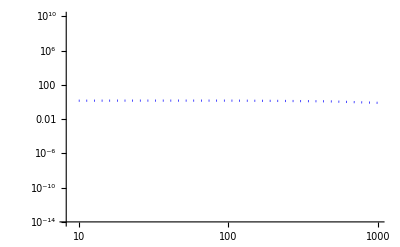

```mathematica
Show[ListLogLogPlot[refdata,PlotRange->{ 10^-14,10^10},PlotStyle-> {Blue,Dotted},Joined->True],ListLogLogPlot[refdata2,PlotRange->{ 10^-14,10^10},PlotStyle->{Red,Dotted},Joined->True]]
```

```mathematica
fileWrite=OpenWrite["VelocityCurve_100MeV_1eV_2.8KeV_200_0.1"] ; 
Write[fileWrite,dataapp] 
Close[fileWrite]
```

VelocityCurve_100MeV_1eV_2.8KeV_200_0.1

```mathematica
vtest=√((8 20 10^-9)/40(299792458/10^3)^2)
```

```mathematica
149896229/(2500000 √10)
```

```mathematica
instepdelta=(Log10[10 10^-3]-Log10[10^-6])/200;
instepmphi=(Log10[100 10^-3]-Log10[100 10^-6])/200;
inputdelta=Table[10^x,{x,Log10[ 7 10^-3],Log10[10 10^-3],instepdelta}]
inputmphi=Table[10^x,{x,Log10[1 10^-3],Log10[2 10^-3],instepmphi}]
```

{7/1000,7/(100 10^(49/50)),7/(100 10^(24/25)),7/(100 10^(47/50)),7/(100 10^(23/25)),7/(100 10^(9/10)),7/(100 10^(22/25)),7/(100 10^(43/50))}

{1/1000,1/(100 10^(197/200)),1/(100 10^(97/100)),1/(100 10^(191/200)),1/(100 10^(47/50)),1/(100 10^(37/40)),1/(100 10^(91/100)),1/(100 10^(179/200)),1/(100 10^(22/25)),1/(100 10^(173/200)),1/(100 10^(17/20)),1/(100 10^(167/200)),1/(100 10^(41/50)),1/(100 10^(161/200)),1/(100 10^(79/100)),1/(100 10^(31/40)),1/(100 10^(19/25)),1/(100 10^(149/200)),1/(100 10^(73/100)),1/(100 10^(143/200)),1/(100 10^(7/10))}

```mathematica
datatest=Table[{i,j,Sigmacalc[160 10^-3,j 10^-3,i 10^-6,60]},{i,inputdelta},{j,inputmphi}]
```

```mathematica
fileread=OpenRead["Ine_DM_XSect_mx-0.010_mphi-delta_60"];
testread=Read[fileread];
Close[fileread]
```

Ine_DM_XSect_mx-0.010_mphi-delta_60

```mathematica
testapp=testread;
```

```mathematica
(*For[i=1,i≤ Length[datatest],i++,
testapp=Append[testapp,Extract[datatest,i]];
];*)
```

```mathematica
deltamphi= {};
For[i=1,i≤ Length[testapp],i++,
For[j=1,j≤Length[Extract[testapp,i]],j++,
If[1≤ Extract[Extract[Extract[Extract[Extract[testapp,i],j],3],1],1]≤ 5,
deltamphi=Append[deltamphi,{Extract[Extract[Extract[testapp,i],j],1] 10^3,Extract[Extract[Extract[testapp,i],j] 10^3,2]}];
];
];
]
```

```mathematica
deltamphi;
```

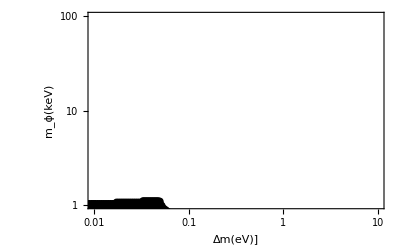

```mathematica
ListLogLogPlot[deltamphi,Frame-> True,FrameLabel->{"Δm(eV)]","m_ϕ(keV)","m_x = 160 MeV    ,    1 ≤ σ/m_x[cm^2/g] ≤ 5    ,    v = 60 km/s"},PlotRange->{{ 10 10^-3,10},{  10 10^-1,100}},PlotStyle->{Black,PointSize[0.013]}]
```

```mathematica
mydata=10.^{{-8.015151289954603*^-8,1.898173841977281},{-8.015151289954603*^-8,1.9131820640816781},{-8.015151289954603*^-8,1.9131820640816781},{-8.015151289954603*^-8,1.9496746589245626},{-8.015151289954603*^-8,1.9496746589245626},{-8.015151289954603*^-8,1.9508054153844832},{-8.015151289954603*^-8,1.9508054153844832},{-8.015151289954603*^-8,1.9788687347988705},{-8.015151289954603*^-8,1.9788687347988705},{-8.015151289954603*^-8,1.994185345028701},{-8.015151289954603*^-8,1.994185345028701},{-8.015151289954603*^-8,2.0034369887916856},{-8.015151289954603*^-8,2.0034369887916856},{-8.015151289954603*^-8,2.009244965154004},{-8.015151289954603*^-8,2.009244965154004},{-8.015151289954603*^-8,2.0192675792305708},{-8.015151289954603*^-8,2.0192675792305708},{-8.015151289954603*^-8,2.032836656749615},{-8.015151289954603*^-8,2.032836656749615},{-8.015151289954603*^-8,2.0447609975996843},{-8.015151289954603*^-8,2.0447609975996843},{-8.015151289954603*^-8,2.0560685621988877},{-8.015151289954603*^-8,2.0560685621988877},{-8.015151289954603*^-8,2.1087001356060897},{-8.015151289954603*^-8,2.1087001356060897},{-8.015151289954603*^-8,2.1150734901983683},{-8.015151289954603*^-8,2.1150734901983683},{-8.015151289954603*^-8,2.138819375856696},{-8.015151289954603*^-8,2.138819375856696},{-8.015151289954603*^-8,2.1422116452364572},{-8.015151289954603*^-8,2.1422116452364572},{-8.015151289954603*^-8,2.299592385249009},{-8.015151289954603*^-8,2.299592385249009},{-0.05982018492993129,2.2925251573745067},{-0.05982018492993129,2.2925251573745067},{-0.08015158462400289,2.2900580523710445},{-0.08015158462400289,2.2900580523710445},{-0.12022733686024789,2.2851238423641194},{-0.12022733686024789,2.2851238423641194},{-0.14901221554165237,2.281423184858925},{-0.14901221554165237,2.281423184858925},{-0.16030308909649293,2.2799583412631192},{-0.16030308909649293,2.2799583412631192},{-0.20037884133273798,2.2746129470889502},{-0.20037884133273798,2.2746129470889502},{-0.23822381439177015,2.2695245430193087},{-0.23822381439177015,2.2695245430193087},{-0.2587704647082043,2.2665948558276967},{-0.2587704647082043,2.2665948558276967},{-0.27835827134320507,2.2637422656674433},{-0.27835827134320507,2.2637422656674433},{-0.31435404587375804,2.2583840219880478},{-0.31435404587375804,2.2583840219880478},{-0.3741056618177885,2.2489653346571203},{-0.3741056618177885,2.2489653346571203},{-0.38588574133254416,2.247063607883618},{-0.38588574133254416,2.247063607883618},{-0.4007576025139632,2.2445965028801553},{-0.4007576025139632,2.2445965028801553},{-0.4214314463799753,2.24111428696381},{-0.4214314463799753,2.24111428696381},{-0.45681082140103535,2.2349465244551534},{-0.45681082140103535,2.2349465244551534},{-0.4809091069864533,2.2305134451520567},{-0.4809091069864533,2.2305134451520567},{-0.49194559344213795,2.2284575243158375},{-0.49194559344213795,2.2284575243158375},{-0.5209848592226983,2.2230350331103104},{-0.5209848592226983,2.2230350331103104},{-0.5610606114589434,2.2149912428386043},{-0.5610606114589434,2.2149912428386043},{-0.5962051676192441,2.2074871317864053},{-0.5962051676192441,2.2074871317864053},{-0.6412121159314335,2.197207527605311},{-0.6412121159314335,2.197207527605311},{-0.6568471384103203,2.1934297730687593},{-0.6568471384103203,2.1934297730687593},{-0.6812878681676785,2.187287709570555},{-0.6812878681676785,2.187287709570555},{-0.6977251884208258,2.18291887779359},{-0.6977251884208258,2.18291887779359},{-0.7068048510368501,2.180451772790127},{-0.7068048510368501,2.180451772790127},{-0.73083464778788,2.1737700300724168},{-0.73083464778788,2.1737700300724168},{-0.7614393726401686,2.164634031856469},{-0.7614393726401686,2.164634031856469},{-0.7717714025135756,2.161331709013292},{-0.7717714025135756,2.161331709013292},{-0.8015151248764136,2.15125769691582},{-0.8015151248764136,2.15125769691582},{-0.8120819736105798,2.1474542433688155},{-0.8120819736105798,2.1474542433688155},{-0.8267190159312396,2.1418004610692134},{-0.8267190159312396,2.1418004610692134},{-0.8415908771126587,2.13594108668599},{-0.8415908771126587,2.13594108668599},{-0.8572846043067351,2.1293107419891837},{-0.8572846043067351,2.1293107419891837},{-0.870630142893219,2.1231943775014326},{-0.870630142893219,2.1231943775014326},{-0.8816666293489037,2.1178489833272636},{-0.8816666293489037,2.1178489833272636},{-0.8867152348552275,2.115330480302896},{-0.8867152348552275,2.115330480302896},{-0.8988866791379153,2.1087001356060897},{-0.8988866791379153,2.1087001356060897},{-0.9146978157623713,2.099448491843105},{-0.9146978157623713,2.099448491843105},{-0.9217423815851488,2.0949254660034238},{-0.9217423815851488,2.0949254660034238},{-0.9406844363530613,2.0809452043171355},{-0.9406844363530613,2.0809452043171355},{-0.9463200890112833,2.0764221784774537},{-0.9463200890112833,2.0764221784774537},{-0.9618181338213938,2.0611055682476236},{-0.9618181338213938,2.0611055682476236},{-0.9638532306146406,2.058741259285972},{-0.9638532306146406,2.058741259285972},{-0.9658883274078873,2.0560685621988877},{-0.9658883274078873,2.0560685621988877},{-0.9810732804036522,2.0307807359133965},{-0.9810732804036522,2.0307807359133965},{-0.9816211910787571,2.029444387369854},{-0.9816211910787571,2.029444387369854},{-0.9869437519226334,2.0034369887916856},{-0.9869437519226334,2.0034369887916856},{-0.9845715749434821,1.981126810654532},{-0.9845715749434821,1.981126810654532},{-1.0018938860576387,1.9752708733354876},{-1.0018938860576387,1.9752708733354876},{-1.0315593354668906,1.9644772889453386},{-1.0315593354668906,1.9644772889453386},{-1.041969638293884,1.9603654472729006},{-1.041969638293884,1.9603654472729006},{-1.0645513854035649,1.9508054153844832},{-1.0645513854035649,1.9508054153844832},{-1.077505559222117,1.9448432449594484},{-1.077505559222117,1.9448432449594484},{-1.082045390530129,1.9426331300605133},{-1.082045390530129,1.9426331300605133},{-1.092220874496363,1.9374419299490606},{-1.092220874496363,1.9374419299490606},{-1.106192596711538,1.9298864208759565},{-1.106192596711538,1.9298864208759565},{-1.122121142766374,1.9201721949248225},{-1.122121142766374,1.9201721949248225},{-1.1331576292220589,1.9126680838726238},{-1.1331576292220589,1.9126680838726238},{-1.1512386815005207,1.898173841977281},{-1.1512386815005207,1.898173841977281},{-1.1576570636946069,1.8922116715522463},{-1.1576570636946069,1.8922116715522463},{-1.162196895002619,1.887585849670754},{-1.162196895002619,1.887585849670754},{-1.1779297586734885,1.866204272974078},{-1.1779297586734885,1.866204272974078},{-1.1863049647072352,1.8455422685700786},{-1.1863049647072352,1.8455422685700786},{-1.1889662451291736,1.8280669414622186},{-1.1889662451291736,1.8280669414622186},{-1.1877138778717908,1.8120307589397115},{-1.1877138778717908,1.8120307589397115},{-1.182547862935087,1.7929106951628764},{-1.182547862935087,1.7929106951628764},{-1.1747988405300318,1.7763605324313148},{-1.1747988405300318,1.7763605324313148},{-1.162196895002619,1.756520896361803},{-1.162196895002619,1.756520896361803},{-1.156013331669292,1.7484000090587386},{-1.156013331669292,1.7484000090587386},{-1.1527879325585533,1.7444630917057542},{-1.1527879325585533,1.7444630917057542},{-1.1562481505300513,1.7402791217556741},{-1.1562481505300513,1.7402791217556741},{-1.1589094309519896,1.7359616879996147},{-1.1589094309519896,1.7359616879996147},{-1.162196895002619,1.7302051096582018},{-1.162196895002619,1.7302051096582018},{-1.1706895104667447,1.698800918884959},{-1.1706895104667447,1.698800918884959},{-1.1704938280827788,1.6876475483484719},{-1.1704938280827788,1.6876475483484719},{-1.1692414608253965,1.678395904585487},{-1.1692414608253965,1.678395904585487},{-1.162196895002619,1.6561919595543237},{-1.162196895002619,1.6561919595543237},{-1.1557785128085327,1.643445250369767},{-1.1557785128085327,1.643445250369767},{-1.1506124978718293,1.6350159749412696},{-1.1506124978718293,1.6350159749412696},{-1.1386593691163136,1.6180620590816313},{-1.1386593691163136,1.6180620590816313},{-1.1438810238633978,1.610961701157509},{-1.1438810238633978,1.610961701157509},{-1.1495166765216198,1.59903736030744},{-1.1495166765216198,1.59903736030744},{-1.1535868701081133,1.5823844015340673},{-1.1535868701081133,1.5823844015340673},{-1.1544087361207707,1.572156195373879},{-1.1544087361207707,1.572156195373879},{-1.1501428601503108,1.5455834185657502},{-1.1501428601503108,1.5455834185657502},{-1.1441158427241571,1.529752828126865},{-1.1441158427241571,1.529752828126865},{-1.1348013612473733,1.5130998693534923},{-1.1348013612473733,1.5130998693534923},{-1.122121142766374,1.4950077659947665},{-1.122121142766374,1.4950077659947665},{-1.1150765769435962,1.4863728984826476},{-1.1150765769435962,1.4863728984826476},{-1.1067796438634363,1.4771212547196628},{-1.1067796438634363,1.4771212547196628},{-1.1020832666482514,1.471981452629116},{-1.1020832666482514,1.471981452629116},{-1.0928470581250544,1.4629354009497528},{-1.0928470581250544,1.4629354009497528},{-1.082045390530129,1.4524245056745841},{-1.082045390530129,1.4524245056745841},{-1.06936517204913,1.4411426400858334},{-1.06936517204913,1.4411426400858334},{-1.0491707500238343,1.4244896813124606},{-1.0491707500238343,1.4244896813124606},{-1.041969638293884,1.4186303069292368},{-1.041969638293884,1.4186303069292368},{-1.031246243652545,1.4104066235843613},{-1.031246243652545,1.4104066235843613},{-1.0192704817538232,1.4016689600304315},{-1.0192704817538232,1.4016689600304315},{-1.0018938860576387,1.3890250468876855},{-1.0018938860576387,1.3890250468876855},{-0.9770030868171584,1.3718581079052583},{-0.9770030868171584,1.3718581079052583},{-0.9618181338213938,1.3617840958077863},{-0.9618181338213938,1.3617840958077863},{-0.9464570666800596,1.3516843846998612},{-0.9464570666800596,1.3516843846998612},{-0.9217423815851488,1.336059386344598},{-0.9217423815851488,1.336059386344598},{-0.9130149472602633,1.3306882931599762},{-0.9130149472602633,1.3306882931599762},{-0.8943468478299033,1.319226534498056},{-0.8943468478299033,1.319226534498056},{-0.8710019394227546,1.305220573801315},{-0.8710019394227546,1.305220573801315},{-0.8658044662012808,1.3021834295581394},{-0.8658044662012808,1.3021834295581394},{-0.8673035423657963,1.3003634608257482},{-0.8673035423657963,1.3003634608257482},{-0.8815100834417309,1.2668005531744755},{-0.8815100834417309,1.2668005531744755},{-0.8815100834417309,1.266389369007232},{-0.8815100834417309,1.266389369007232},{-0.8770485250873052,1.2200283541504973},{-0.8770485250873052,1.2200283541504973},{-0.8747981776716958,1.2139633876836515},{-0.8747981776716958,1.2139633876836515},{-0.861041706078883,1.1884185712936324},{-0.861041706078883,1.1884185712936324},{-0.8415908771126587,1.1627709588618025},{-0.8415908771126587,1.1627709588618025},{-0.8403776463320692,1.1613318142764493},{-0.8403776463320692,1.1613318142764493},{-0.8188134476190116,1.1386138890362314},{-0.8188134476190116,1.1386138890362314},{-0.8015151248764136,1.1225777065137243},{-0.8015151248764136,1.1225777065137243},{-0.7853908964376117,1.108700240869247},{-0.7853908964376117,1.108700240869247},{-0.770558171732986,1.0967245019982723},{-0.770558171732986,1.0967245019982723},{-0.7614393726401686,1.0895801770924116},{-0.7614393726401686,1.0895801770924116},{-0.7451977347709873,1.077398846137815},{-0.7451977347709873,1.077398846137815},{-0.7282418562003298,1.0651018696361811},{-0.7282418562003298,1.0651018696361811},{-0.715258330024183,1.0560686674620448},{-0.715258330024183,1.0560686674620448},{-0.6812878681676785,1.0333507422218269},{-0.6812878681676785,1.0333507422218269},{-0.6660246422183274,1.023482322207976},{-0.6660246422183274,1.023482322207976},{-0.6476304981255194,1.0118663694833399},{-0.6476304981255194,1.0118663694833399},{-0.6412121159314335,1.0078573238527129},{-0.6412121159314335,1.0078573238527129},{-0.6211742398133109,0.9955217988353999},{-0.6211742398133109,0.9955217988353999},{-0.5905695149610222,0.9771213073512414},{-0.5905695149610222,0.9771213073512414},{-0.5734277381255972,0.9670472952537692},{-0.5734277381255972,0.9670472952537692},{-0.5610606114589434,0.9598258733165503},{-0.5610606114589434,0.9598258733165503},{-0.5283425168598215,0.9411426927174116},{-0.5283425168598215,0.9411426927174116},{-0.5026689880834769,0.9267512468638799},{-0.5026689880834769,0.9267512468638799},{-0.45093056576285595,0.898173947240438},{-0.45093056576285595,0.898173947240438},{-0.44380772698649207,0.8942676976516222},{-0.44380772698649207,0.8942676976516222},{-0.4007576025139632,0.8710100931918965},{-0.4007576025139632,0.8710100931918965},{-0.38699134680195224,0.8636216276867351},{-0.38699134680195224,0.8636216276867351},{-0.36068185027771815,0.8496285164952206},{-0.36068185027771815,0.8496285164952206},{-0.29899297873242386,0.8171578167881894},{-0.29899297873242386,0.8171578167881894},{-0.27254650453941354,0.8033959966907496},{-0.27254650453941354,0.8033959966907496},{-0.25239121899091144,0.7929108004260336},{-0.25239121899091144,0.7929108004260336},{-0.24045459356898302,0.7867173389069244},{-0.24045459356898302,0.7867173389069244},{-0.20037884133273798,0.7660810335133776},{-0.20037884133273798,0.7660810335133776},{-0.1667997442441655,0.7488112984891395},{-0.1667997442441655,0.7488112984891395},{-0.12022733686024789,0.7250140148099065},{-0.12022733686024789,0.7250140148099065},{-0.04196416739303016,0.6851676991029402},{-0.04196416739303016,0.6851676991029402},{-8.015151289954603*^-8,0.6640045639951124},{-8.015151289954603*^-8,0.6640045639951124},{-8.015151289954603*^-8,0.6876476536116292},{-8.015151289954603*^-8,0.6876476536116292},{-8.015151289954603*^-8,0.7929108004260336},{-8.015151289954603*^-8,0.7929108004260336},{-8.015151289954603*^-8,0.8507849719655938},{-8.015151289954603*^-8,0.8507849719655938},{-8.015151289954603*^-8,0.898173947240438},{-8.015151289954603*^-8,0.898173947240438},{-8.015151289954603*^-8,0.9008466443275225},{-8.015151289954603*^-8,0.9008466443275225},{-8.015151289954603*^-8,0.9508055206476402},{-8.015151289954603*^-8,0.9508055206476402},{-8.015151289954603*^-8,0.9518334810657496},{-8.015151289954603*^-8,0.9518334810657496},{-8.015151289954603*^-8,0.9651841169959458},{-8.015151289954603*^-8,0.9651841169959458},{-8.015151289954603*^-8,0.9771213073512414},{-8.015151289954603*^-8,0.9771213073512414},{-8.015151289954603*^-8,1.0034370940548425},{-8.015151289954603*^-8,1.0034370940548425},{-8.015151289954603*^-8,1.0085768961453896},{-8.015151289954603*^-8,1.0085768961453896},{-8.015151289954603*^-8,1.042037007754851},{-8.015151289954603*^-8,1.042037007754851},{-8.015151289954603*^-8,1.0560686674620448},{-8.015151289954603*^-8,1.0560686674620448},{-8.015151289954603*^-8,1.0879354404234367},{-8.015151289954603*^-8,1.0879354404234367},{-8.015151289954603*^-8,1.108700240869247},{-8.015151289954603*^-8,1.108700240869247},{-8.015151289954603*^-8,1.1184658648412864},{-8.015151289954603*^-8,1.1184658648412864},{-8.015151289954603*^-8,1.1294650413150573},{-8.015151289954603*^-8,1.1294650413150573},{-8.015151289954603*^-8,1.1520801705134645},{-8.015151289954603*^-8,1.1520801705134645},{-8.015151289954603*^-8,1.1613318142764493},{-8.015151289954603*^-8,1.1613318142764493},{-8.015151289954603*^-8,1.1937896644782542},{-8.015151289954603*^-8,1.1937896644782542},{-8.015151289954603*^-8,1.2139633876836515},{-8.015151289954603*^-8,1.2139633876836515},{-8.015151289954603*^-8,1.2579086955578291},{-8.015151289954603*^-8,1.2579086955578291},{-8.015151289954603*^-8,1.2665949610908538},{-8.015151289954603*^-8,1.2665949610908538},{-8.015151289954603*^-8,1.2986544766306412},{-8.015151289954603*^-8,1.2986544766306412},{-8.015151289954603*^-8,1.319226534498056},{-8.015151289954603*^-8,1.319226534498056},{-8.015151289954603*^-8,1.3331040001425334},{-8.015151289954603*^-8,1.3331040001425334},{-8.015151289954603*^-8,1.3619639888809552},{-8.015151289954603*^-8,1.3619639888809552},{-8.015151289954603*^-8,1.3718581079052583},{-8.015151289954603*^-8,1.3718581079052583},{-8.015151289954603*^-8,1.3889222508458747},{-8.015151289954603*^-8,1.3889222508458747},{-8.015151289954603*^-8,1.3981738946088593},{-8.015151289954603*^-8,1.3981738946088593},{-8.015151289954603*^-8,1.4244896813124606},{-8.015151289954603*^-8,1.4244896813124606},{-8.015151289954603*^-8,1.4771212547196628},{-8.015151289954603*^-8,1.4771212547196628},{-8.015151289954603*^-8,1.529752828126865},{-8.015151289954603*^-8,1.529752828126865},{-8.015151289954603*^-8,1.5410603927260689},{-8.015151289954603*^-8,1.5410603927260689},{-8.015151289954603*^-8,1.6350159749412696},{-8.015151289954603*^-8,1.6350159749412696},{-8.015151289954603*^-8,1.7207478738115949},{-8.015151289954603*^-8,1.7207478738115949},{-8.015151289954603*^-8,1.7402791217556741},{-8.015151289954603*^-8,1.7402791217556741},{-8.015151289954603*^-8,1.8455422685700786},{-8.015151289954603*^-8,1.8455422685700786},{-8.015151289954603*^-8,1.8776403326255455},{-8.015151289954603*^-8,1.8776403326255455},{-8.015151289954603*^-8,1.8852215407091024},{-8.015151289954603*^-8,1.8852215407091024},{-8.015151289954603*^-8,1.898173841977281},{-8.015151289954603*^-8,1.898173841977281},{-8.015151289954603*^-8,1.8852215407091024},{-8.015151289954603*^-8,1.8776403326255455},{-8.015151289954603*^-8,1.8455422685700786},{-8.015151289954603*^-8,1.7402791217556741},{-8.015151289954603*^-8,1.7207478738115949},{-8.015151289954603*^-8,1.6350159749412696},{-8.015151289954603*^-8,1.5410603927260689},{-8.015151289954603*^-8,1.529752828126865},{-8.015151289954603*^-8,1.4771212547196628},{-8.015151289954603*^-8,1.4244896813124606},{-8.015151289954603*^-8,1.3981738946088593},{-8.015151289954603*^-8,1.3889222508458747},{-8.015151289954603*^-8,1.3718581079052583},{-8.015151289954603*^-8,1.3619639888809552},{-8.015151289954603*^-8,1.3331040001425334},{-8.015151289954603*^-8,1.319226534498056},{-8.015151289954603*^-8,1.2986544766306412},{-8.015151289954603*^-8,1.2665949610908538},{-8.015151289954603*^-8,1.2579086955578291},{-8.015151289954603*^-8,1.2139633876836515},{-8.015151289954603*^-8,1.1937896644782542},{-8.015151289954603*^-8,1.1613318142764493},{-8.015151289954603*^-8,1.1520801705134645},{-8.015151289954603*^-8,1.1294650413150573},{-8.015151289954603*^-8,1.1184658648412864},{-8.015151289954603*^-8,1.108700240869247},{-8.015151289954603*^-8,1.0879354404234367},{-8.015151289954603*^-8,1.0560686674620448},{-8.015151289954603*^-8,1.042037007754851},{-8.015151289954603*^-8,1.0085768961453896},{-8.015151289954603*^-8,1.0034370940548425},{-8.015151289954603*^-8,0.9771213073512414},{-8.015151289954603*^-8,0.9651841169959458},{-8.015151289954603*^-8,0.9518334810657496},{-8.015151289954603*^-8,0.9508055206476402},{-8.015151289954603*^-8,0.9008466443275225},{-8.015151289954603*^-8,0.898173947240438},{-8.015151289954603*^-8,0.8507849719655938},{-8.015151289954603*^-8,0.7929108004260336},{-8.015151289954603*^-8,0.6876476536116292},{-8.015151289954603*^-8,0.6640045639951124},{-0.04196416739303016,0.6851676991029402},{-0.12022733686024789,0.7250140148099065},{-0.1667997442441655,0.7488112984891395},{-0.20037884133273798,0.7660810335133776},{-0.24045459356898302,0.7867173389069244},{-0.25239121899091144,0.7929108004260336},{-0.27254650453941354,0.8033959966907496},{-0.29899297873242386,0.8171578167881894},{-0.36068185027771815,0.8496285164952206},{-0.38699134680195224,0.8636216276867351},{-0.4007576025139632,0.8710100931918965},{-0.44380772698649207,0.8942676976516222},{-0.45093056576285595,0.898173947240438},{-0.5026689880834769,0.9267512468638799},{-0.5283425168598215,0.9411426927174116},{-0.5610606114589434,0.9598258733165503},{-0.5734277381255972,0.9670472952537692},{-0.5905695149610222,0.9771213073512414},{-0.6211742398133109,0.9955217988353999},{-0.6412121159314335,1.0078573238527129},{-0.6476304981255194,1.0118663694833399},{-0.6660246422183274,1.023482322207976},{-0.6812878681676785,1.0333507422218269},{-0.715258330024183,1.0560686674620448},{-0.7282418562003298,1.0651018696361811},{-0.7451977347709873,1.077398846137815},{-0.7614393726401686,1.0895801770924116},{-0.770558171732986,1.0967245019982723},{-0.7853908964376117,1.108700240869247},{-0.8015151248764136,1.1225777065137243},{-0.8188134476190116,1.1386138890362314},{-0.8403776463320692,1.1613318142764493},{-0.8415908771126587,1.1627709588618025},{-0.861041706078883,1.1884185712936324},{-0.8747981776716958,1.2139633876836515},{-0.8770485250873052,1.2200283541504973},{-0.8815100834417309,1.266389369007232},{-0.8815100834417309,1.2668005531744755},{-0.8673035423657963,1.3003634608257482},{-0.8658044662012808,1.3021834295581394},{-0.8710019394227546,1.305220573801315},{-0.8943468478299033,1.319226534498056},{-0.9130149472602633,1.3306882931599762},{-0.9217423815851488,1.336059386344598},{-0.9464570666800596,1.3516843846998612},{-0.9618181338213938,1.3617840958077863},{-0.9770030868171584,1.3718581079052583},{-1.0018938860576387,1.3890250468876855},{-1.0192704817538232,1.4016689600304315},{-1.031246243652545,1.4104066235843613},{-1.041969638293884,1.4186303069292368},{-1.0491707500238343,1.4244896813124606},{-1.06936517204913,1.4411426400858334},{-1.082045390530129,1.4524245056745841},{-1.0928470581250544,1.4629354009497528},{-1.1020832666482514,1.471981452629116},{-1.1067796438634363,1.4771212547196628},{-1.1150765769435962,1.4863728984826476},{-1.122121142766374,1.4950077659947665},{-1.1348013612473733,1.5130998693534923},{-1.1441158427241571,1.529752828126865},{-1.1501428601503108,1.5455834185657502},{-1.1544087361207707,1.572156195373879},{-1.1535868701081133,1.5823844015340673},{-1.1495166765216198,1.59903736030744},{-1.1438810238633978,1.610961701157509},{-1.1386593691163136,1.6180620590816313},{-1.1506124978718293,1.6350159749412696},{-1.1557785128085327,1.643445250369767},{-1.162196895002619,1.6561919595543237},{-1.1692414608253965,1.678395904585487},{-1.1704938280827788,1.6876475483484719},{-1.1706895104667447,1.698800918884959},{-1.162196895002619,1.7302051096582018},{-1.1589094309519896,1.7359616879996147},{-1.1562481505300513,1.7402791217556741},{-1.1527879325585533,1.7444630917057542},{-1.156013331669292,1.7484000090587386},{-1.162196895002619,1.756520896361803},{-1.1747988405300318,1.7763605324313148},{-1.182547862935087,1.7929106951628764},{-1.1877138778717908,1.8120307589397115},{-1.1889662451291736,1.8280669414622186},{-1.1863049647072352,1.8455422685700786},{-1.1779297586734885,1.866204272974078},{-1.162196895002619,1.887585849670754},{-1.1576570636946069,1.8922116715522463},{-1.1512386815005207,1.898173841977281},{-1.1331576292220589,1.9126680838726238},{-1.122121142766374,1.9201721949248225},{-1.106192596711538,1.9298864208759565},{-1.092220874496363,1.9374419299490606},{-1.082045390530129,1.9426331300605133},{-1.077505559222117,1.9448432449594484},{-1.0645513854035649,1.9508054153844832},{-1.041969638293884,1.9603654472729006},{-1.0315593354668906,1.9644772889453386},{-1.0018938860576387,1.9752708733354876},{-0.9845715749434821,1.981126810654532},{-0.9869437519226334,2.0034369887916856},{-0.9816211910787571,2.029444387369854},{-0.9810732804036522,2.0307807359133965},{-0.9658883274078873,2.0560685621988877},{-0.9638532306146406,2.058741259285972},{-0.9618181338213938,2.0611055682476236},{-0.9463200890112833,2.0764221784774537},{-0.9406844363530613,2.0809452043171355},{-0.9217423815851488,2.0949254660034238},{-0.9146978157623713,2.099448491843105},{-0.8988866791379153,2.1087001356060897},{-0.8867152348552275,2.115330480302896},{-0.8816666293489037,2.1178489833272636},{-0.870630142893219,2.1231943775014326},{-0.8572846043067351,2.1293107419891837},{-0.8415908771126587,2.13594108668599},{-0.8267190159312396,2.1418004610692134},{-0.8120819736105798,2.1474542433688155},{-0.8015151248764136,2.15125769691582},{-0.7717714025135756,2.161331709013292},{-0.7614393726401686,2.164634031856469},{-0.73083464778788,2.1737700300724168},{-0.7068048510368501,2.180451772790127},{-0.6977251884208258,2.18291887779359},{-0.6812878681676785,2.187287709570555},{-0.6568471384103203,2.1934297730687593},{-0.6412121159314335,2.197207527605311},{-0.5962051676192441,2.2074871317864053},{-0.5610606114589434,2.2149912428386043},{-0.5209848592226983,2.2230350331103104},{-0.49194559344213795,2.2284575243158375},{-0.4809091069864533,2.2305134451520567},{-0.45681082140103535,2.2349465244551534},{-0.4214314463799753,2.24111428696381},{-0.4007576025139632,2.2445965028801553},{-0.38588574133254416,2.247063607883618},{-0.3741056618177885,2.2489653346571203},{-0.31435404587375804,2.2583840219880478},{-0.27835827134320507,2.2637422656674433},{-0.2587704647082043,2.2665948558276967},{-0.23822381439177015,2.2695245430193087},{-0.20037884133273798,2.2746129470889502},{-0.16030308909649293,2.2799583412631192},{-0.14901221554165237,2.281423184858925},{-0.12022733686024789,2.2851238423641194},{-0.08015158462400289,2.2900580523710445},{-0.05982018492993129,2.2925251573745067},{-8.015151289954603*^-8,2.299592385249009},{-8.015151289954603*^-8,2.1422116452364572},{-8.015151289954603*^-8,2.138819375856696},{-8.015151289954603*^-8,2.1150734901983683},{-8.015151289954603*^-8,2.1087001356060897},{-8.015151289954603*^-8,2.0560685621988877},{-8.015151289954603*^-8,2.0447609975996843},{-8.015151289954603*^-8,2.032836656749615},{-8.015151289954603*^-8,2.0192675792305708},{-8.015151289954603*^-8,2.009244965154004},{-8.015151289954603*^-8,2.0034369887916856},{-8.015151289954603*^-8,1.994185345028701},{-8.015151289954603*^-8,1.9788687347988705},{-8.015151289954603*^-8,1.9508054153844832},{-8.015151289954603*^-8,1.9496746589245626},{-8.015151289954603*^-8,1.9131820640816781}};
```

```mathematica
deltamphia={};
For[i=1,i≤ Length[testapp],i++,
For[j=1,j≤Length[Extract[testapp,i]],j++,
If[1≤ Extract[Extract[Extract[Extract[Extract[testapp,i],j],3],1],1]≤ 5,
If[ Im[Extract[Extract[Extract[Extract[Extract[testapp,i],j],3],2],1]]≠ 0 ,
deltamphia=Append[deltamphia,{Extract[Extract[Extract[testapp,i],j],1] 10^3,Extract[Extract[Extract[testapp,i],j],2] 10^3}];
];
];
 ];
];
```

```mathematica
deltamphib={};
For[i=1,i≤ Length[testapp],i++,
For[j=1,j≤Length[Extract[testapp,i]],j++,
If[1≤ Extract[Extract[Extract[Extract[Extract[testapp,i],j],3],1],1]≤ 5,
If[ Im[Extract[Extract[Extract[Extract[Extract[testapp,i],j],3],2],1]]== 0 ,
deltamphib=Append[deltamphib,{Extract[Extract[Extract[testapp,i],j],1] 10^3,Extract[Extract[Extract[testapp,i],j],2] 10^3}];
];
];
 ];
];
```

```mathematica
deltamphic={};
For[i=1,i≤ Length[testapp],i++,
For[j=1,j≤Length[Extract[testapp,i]],j++,
If[1≤ Extract[Extract[Extract[Extract[Extract[testapp,i],j],3],1],1]≤ 5,
If[ Im[Extract[Extract[Extract[Extract[Extract[testapp,i],j],3],2],1]]== 0 ,
deltamphic=Append[deltamphic,{Extract[Extract[Extract[testapp,i],j],1] 10^3,Extract[Extract[Extract[testapp,i],j],2] 10^3,Extract[Extract[Extract[Extract[Extract[testapp,i],j],3],1],1],Extract[Extract[Extract[Extract[Extract[testapp,i],j],3],2],1]}];
];
];
 ];
];
```

```mathematica
dm=10;
condata=Table[{Extract[Extract[deltamphic,i],4]/Extract[Extract[deltamphic,i],3],√((Extract[Extract[deltamphic,i],1] 10^-6)/dm)299792.458},{i,1,Length[deltamphic]}];
```

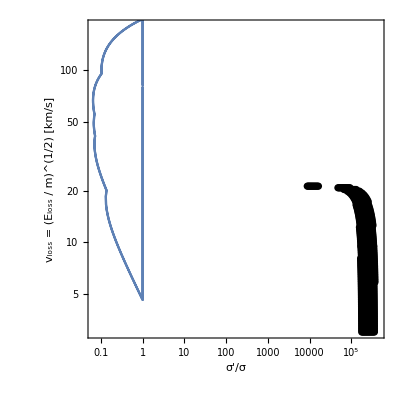

```mathematica
Show[ListLogLogPlot[mydata,Joined-> True],ListLogLogPlot[condata,PlotStyle->{Thick,Black,PointSize[0.013]}],AspectRatio->1,Frame-> True,FrameLabel->{"σ'/σ","v_loss = (E_loss / m)^(1/2) [km/s]"},PlotRange-> {{-2.7,13},{1.1,5.2}}]
```

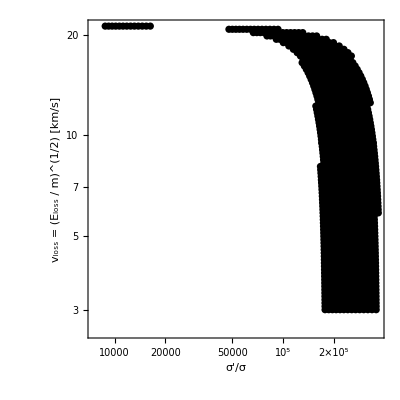

```mathematica
ListLogLogPlot[condata,AspectRatio->1,PlotStyle->{Thick,Black,PointSize[0.013]},Frame-> True,FrameLabel->{"σ'/σ","v_loss = (E_loss / m)^(1/2) [km/s]"}]
```

```mathematica
PowerTicks[label_][min_,max_]:=Block[{min10,max10},min10=Floor[Log10[min]];
max10=Ceiling[Log10[max]];
Join[Table[{10^i,If[label,Superscript["10",i]],{0.015,0},{Thickness[0.0035]}},{i,min10,max10}],Flatten[Table[{k 10^i,Spacer[{0,0}],{0.005,0},{Thickness[0.0035]}},{i,min10,max10},{k,9}],1]]];
```

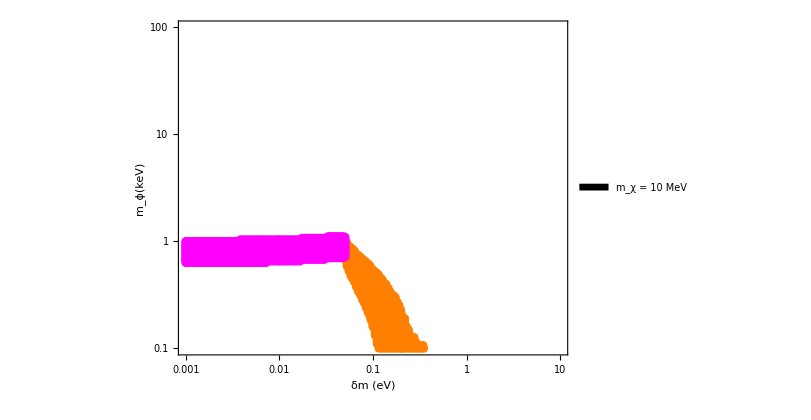

```mathematica
Show[ListLogLogPlot[deltamphia,PlotRange->{{     10^-3,10},{  10^-1, 100}},PlotStyle->{Orange,PointSize[0.00983]},PlotLegends-> Placed[SwatchLegend[{Black}, { Style["m_χ = 10 MeV",Black,FontSize->25]},LegendLayout->"Column",LegendMarkerSize-> {0.1,0.1}],{0.20,0.85}],FrameTicks-> {{PowerTicks[True],Automatic},{PowerTicks[True],Automatic}}] , ListLogLogPlot[deltamphib,PlotStyle->{Magenta,PointSize[0.011]}],Frame-> True,FrameStyle-> Directive[Thickness[0.0035],Black,FontSize-> 20],FrameLabel->{"δm (eV)","m_ϕ(keV)"},ImageSize-> 600, AspectRatio-> 0.7]
```